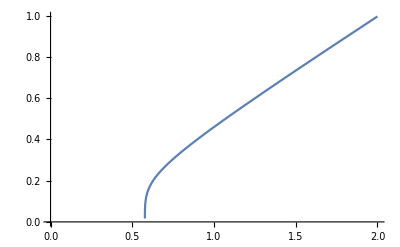

```mathematica
Plot[(((3*frc^2-1) frc^2)/((14/5)* (1.0/4.716)^2*(2*π)^2*9))^(1/4), {frc, 0,2}, MaxRecursion->5, PlotPoints->500]
```

```mathematica
((((3*frc^2-1) frc^2)/((14/5)* (1.0/4.716)^2*(2*π)^2*9))^(1/4))/.{frc->0.6}//N
```

0.159292

```mathematica
frcrecEqn=(3 frc^2-1)/((14/5) (1/4.716)^2 (2 π)^2)==(9 frc^4)/rec^2
```

0.201201 (-1+3 frc^2)==(9 frc^4)/rec^2

```mathematica
Solve[frcrecEqn, rec]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rec→-(6.68816 frc^2)/(√(-1.+3. frc^2))},{rec→(6.68816 frc^2)/(√(-1.+3. frc^2))}}

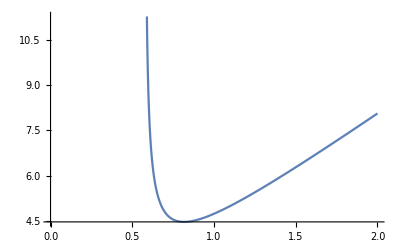

```mathematica
Plot[(6.688155198248582 frc^2)/(√(-1.+3. frc^2)), {frc,0,2}]
```

```mathematica
frcrecEqn2=(3 frc^2-1)/((14/5) (1/lp)^2 (2 π)^2)==(9 frc^4)/rec^2
```

(5 (-1+3 frc^2) lp^2)/(56 π^2)==(9 frc^4)/rec^2

```mathematica
Solve[frcrecEqn2, rec]//Simplify
```

{{rec→-(6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))},{rec→(6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))}}

```mathematica
D[((6.688155198248582 frc^2)/(√(-1.+3. frc^2))), frc]//Simplify
```

(-4.45877 frc+6.68816 frc^3)/((-0.333333+1. frc^2) √(-1.+3. frc^2))

```mathematica
NSolve[(-4.4587701321657205 frc+6.68815519824858 frc^3)/((-0.3333333333333333+1. frc^2) √(-1.+3. frc^2))==0, frc]
```

{{frc→0.816497},{frc→-0.816497},{frc→0.}}

```mathematica
(6.688155198248582 frc^2)/(√(-1.+3. frc^2))/.{frc->0.8164965809277263}
```

4.45877

```mathematica
<<MaTeX`
```

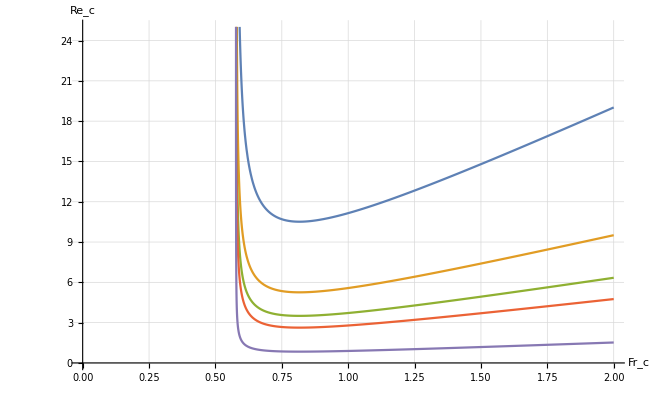

```mathematica
Plot[{(6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))/.{lp->2.0}, (6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))/.{lp->4.0}, (6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))/.{lp->6.0}, (6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))/.{lp->8.0}, (6 √(14/5) frc^2 π)/(√((-1+3 frc^2) lp^2))/.{lp->25.0}},{frc,0,2},GridLines->Automatic, AxesLabel->{Style["Fr_c",21,FontFamily->"Times"],Style["Re_c", 21,FontFamily->"Times"]}, PlotLegends->{MaTeX["S_o\lambda/H=2",Magnification->1.6],MaTeX["S_o\lambda/H=4",Magnification->1.6], MaTeX["S_o\lambda/H=6",Magnification->1.6], MaTeX["S_o\lambda/H=8",Magnification->1.6], MaTeX["S_o\lambda/H=25",Magnification->1.6]},PlotRange->{{0,2},{0,Automatic}}, ImageSize->Large, PlotPoints->120,TicksStyle->{{FontSize->17,FontFamily->"Times"},{FontSize->17,FontFamily->"Times"}}]
```